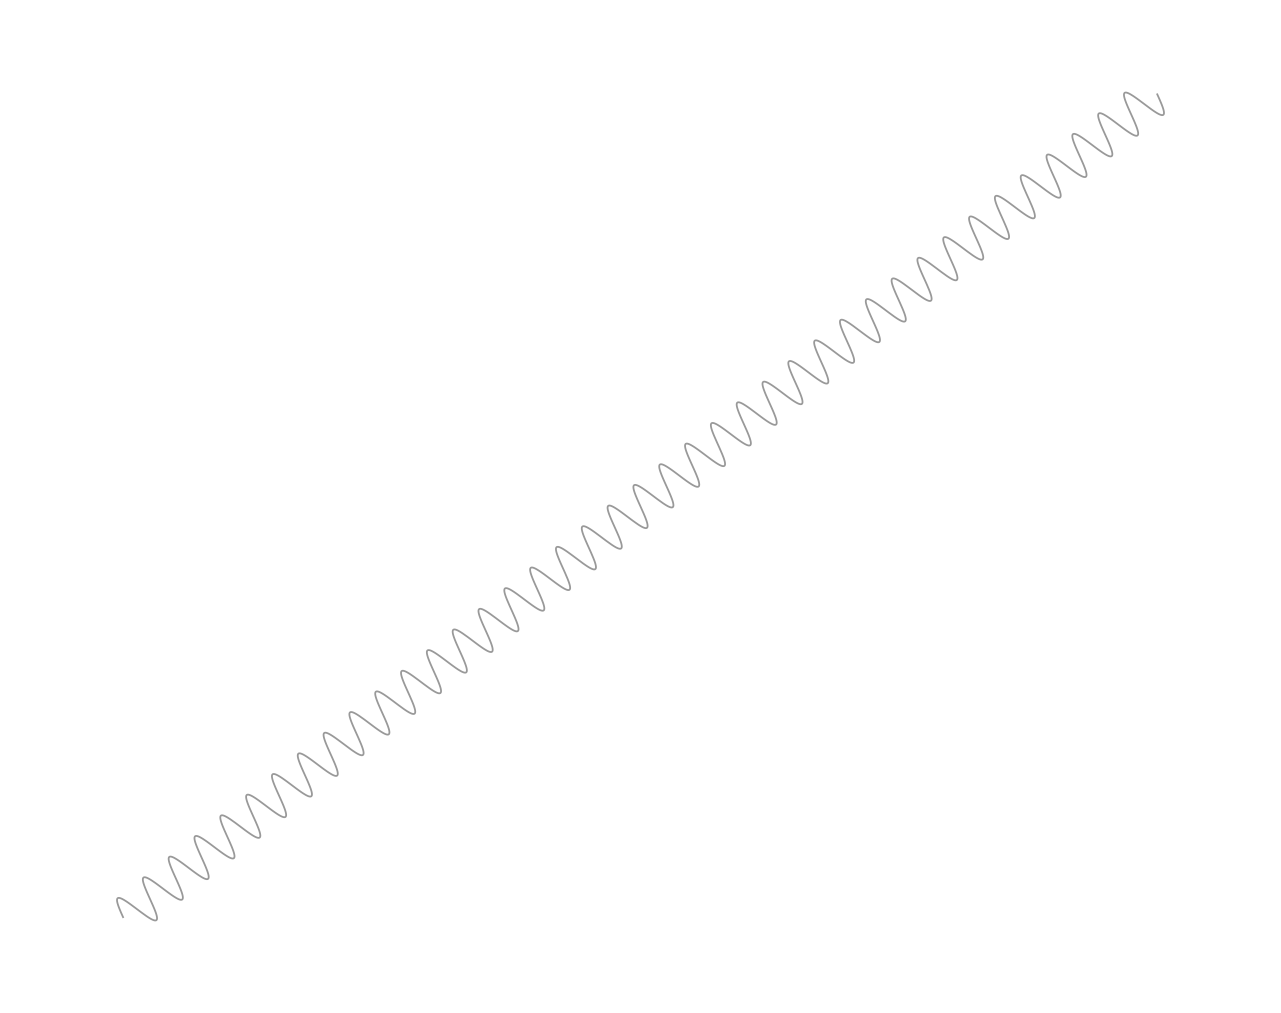

```mathematica
SlikaVzmeti[r2_,ravna_,n_,R_,barva_]:=ParametricPlot[
RotationMatrix[{{1,0},r2}].Which[
u≤ravna,{u,0},
ravna<u<Norm[r2]-ravna,{u,R Sin[(2π n)/(Norm[r2]-2ravna)(u-ravna)]},
Norm[r2]-ravna≤u, {u,0}
],
{u,0,Norm[r2]},
Axes->False,
PlotStyle->Directive[RGBColor[barva],Thickness[faktordebelina*.002]]
];
r2={5,4};
ravna=0;
n=40;
R=.1;
barva=.6{1,1,1};
SlikaVzmeti[r2,ravna,n,R,barva]
```

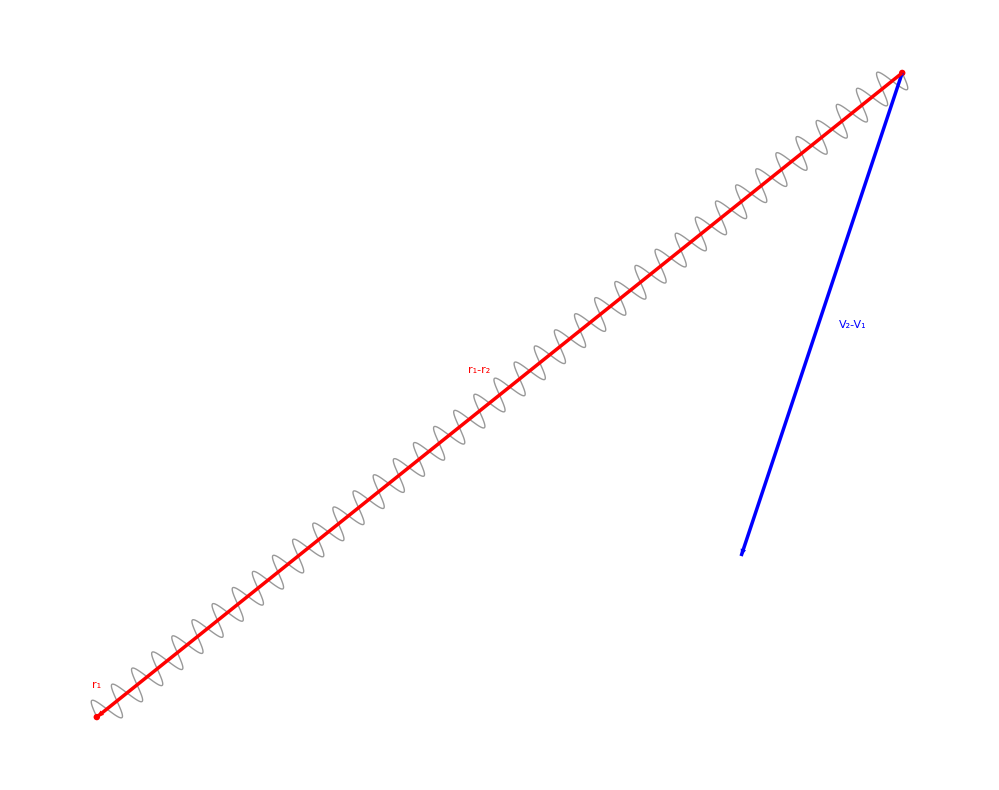

```mathematica
velčrk=7;
faktordebelina=.5;
Show[


SlikaVzmeti[r2,ravna,n,R,barva],
Graphics[{
RGBColor[{1,0,0}],
Style[Text[
If[#=={0,0},"r_1","r_2"],
#+{0,+.2}
],
Red,velčrk,Bold,FontFamily->"Comic Sans MS"],
Disk[#,.02]
}]&/@{
{0,0},
r2
},

ΔV={-1,-3};
Graphics[{
Style[
Rotate[Text[
"V_2-V_1",
(2r2+ΔV)/2+RotationMatrix[{{1,0},ΔV}].{0,.2}
],VectorAngle[{1,0},-ΔV]],
Blue,velčrk,Bold,FontFamily->"Comic Sans MS"],
RGBColor[{0,0,1}],
Arrowheads[faktordebelina*.03],
Thickness[faktordebelina*.005],
Arrow[{r2,r2+ΔV}]
}],

Graphics[{
Style[
Rotate[Text[
"r_1-r_2",
r2/2+RotationMatrix[{{1,0},r2}].{0,.2}
],VectorAngle[{1,0},r2]],
Red,velčrk,Bold,FontFamily->"Comic Sans MS"],
RGBColor[{1,0,0}],
Arrowheads[faktordebelina*.03],
Thickness[faktordebelina*.005],
Arrow[{r2,{0,0}}]
}]





(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)

]
```

```mathematica
Export["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\zavorna sila vzmeti.pdf",%]
```

c:\Users\gal\Downloads\rn.aviončki\grafi\zavorna sila vzmeti.pdf